Estimate parameters

z_(t+1)=μ+ϕ z_t+σ ϵ_t

```mathematica
Clear["Global`*"];
```

```mathematica
SetDirectory[NotebookDirectory[]];
<<"Sampler1`";
INTERVAL=1001;
```

```mathematica
SeedRandom[0];
```

```mathematica
csv = Import["./covid19_confirmed.csv","CSV"];
```

```mathematica
csv[[;;,1]]
```

{China,France,Japan,Russia,United Kingdom,US,Brazil,India,South Africa,Korea, South,Vietnam}

```mathematica
x=N[1+csv[[10,2;;]]];
```

```mathematica
y1=Drop[x,1];
y=Drop[x,-1];
z=(y1-y)/y;
ζ1=Drop[z,1];
ζ=Drop[z,-1];
```

```mathematica
Length[ζ]
```

336

```mathematica
UP[a_,b_,c_,c1_,d_,σ_]=a^2/2+b^2/2+c1^2/2+c^2/2+d^2/2+σ^2/2;
```

μ = a t + b+ a1 t^2
ϕ = c t + d
σ = e t + f

```mathematica
loss[a_,b_,c_,χ_,d_,σ_]=Simplify[Sum[1/2(1/σ(ζ1[[i]]-( a i/Length[ζ]+b)-(c i/Length[ζ]+χ( i/Length[ζ])^2+d) ζ[[i]]))^2+Log[√(2 π) ]+1/2 Log[(σ)^2],{i,1,Length[ζ]}]];
```

```mathematica
U[a_,b_,c_,χ_,d_,σ_]=N[Simplify[loss[a,b,c,χ,d,σ]+UP[a,b,c,χ,d,σ]]];
```

```mathematica
dU[a_,b_,c_,c1_,d_,σ_]=Simplify[GradientG[U[a,b,c,c1,d,σ],{a,b,c,c1,d,σ}]];
```

```mathematica
ddU[a_,b_,c_,c1_,d_,σ_]=Simplify[HessianH[U[a,b,c,c1,d,σ],{a,b,c,c1,d,σ}]];
```

```mathematica
QS=hmc[U,dU,ddU,6,5000,10000,True,True];
```

1001 465.201 32.8774 0.332149 0.446483 -1155.06 -689.862 -212.542 0.00033493 0.0166745 True {1,2,3,6,11} {1,11}

2002 738.17 12.271 0.35596 0.451103 -1451.19 -1220.8 -713.024 0.000445792 0.018342 False {1,7,10,11} {1,11}

3003 197.861 31.6505 0.33616 0.398787 -1460.31 -1262.45 -1112.45 0.000405265 0.032494 True {1,2,3,5,9,11} {1,11}

4004 265.14 11.3791 0.410762 0.414889 -1464.56 -1280.52 -1199.42 0.000490371 0.032494 False {1,3,5,6,7} {1,11}

5005 141.044 28.3574 0.447913 0.425856 -1452.04 -1311. -1245.69 0.000490371 0.0432495 True {1,5,6,11} {1,11}

6006 211.859 6.29489 0.420997 0.452609 -1457.55 -1311. -1245.69 0.000490371 0.0432495 False {1,5,6,7} {1,11}

7007 149.66 28.6263 0.502615 0.414869 -1460.66 -1311. -1245.69 0.000490371 0.0432495 True {1,2,3,4,5,6,7} {1,11}

8008 210.808 9.88565 0.410844 0.45387 -1456.5 -1311. -1245.69 0.000490371 0.0432495 False {1,4,10,11} {1,11}

9009 151.182 23.0997 0.397099 0.392752 -1462.18 -1311. -1245.69 0.000490371 0.0432495 True {1,2,4,5,7} {1,11}

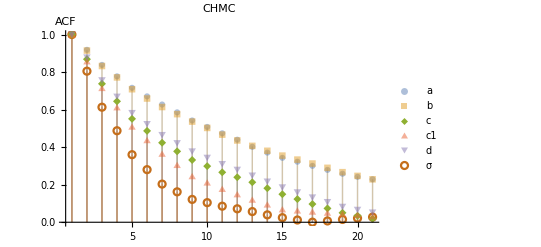

```mathematica
QS1=Table[QS[[i]],{i,1,50000,10}];
ListPlot[Table[CorrelationFunction[QS1[[;;,i]],{20}],{i,1,6}],Filling->Axis,PlotRange->All,AxesLabel->{None,"ACF"},PlotLabel->CHMC,PlotLegends->{a,b,c,c1,d,σ},PlotMarkers->Automatic,PlotStyle->{Opacity[.5],Opacity[.5],Opacity[1]}]
```

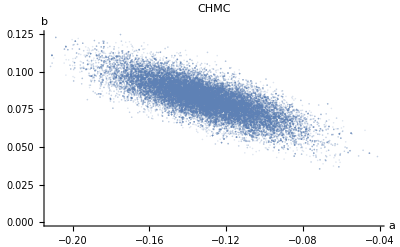

```mathematica
ListPlot[QS[[All,1;;2]],AxesLabel->{a,b},PlotLabel->"CHMC",PlotStyle->Opacity[0.2]]
```

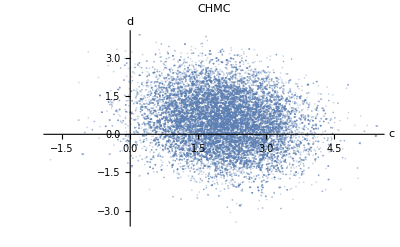

```mathematica
ListPlot[QS[[All,3;;4]],AxesLabel->{c,d},PlotLabel->"CHMC",PlotStyle->Opacity[0.2]]
```

```mathematica
t=Table[i ,{i,0,1,0.1}];
```

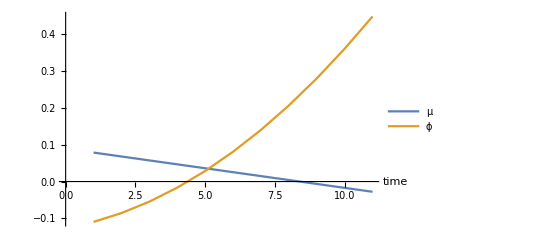

```mathematica
y=QS[[1,1]] t + QS[[1,2]];
y2=QS[[1,3]] t + QS[[1,4]]+t^2 QS[[1,5]];
ListPlot[{y,y2},Joined->True,Ticks->{None,Automatic},AxesLabel->{"time"},PlotLegends->{"μ","ϕ"}]
```

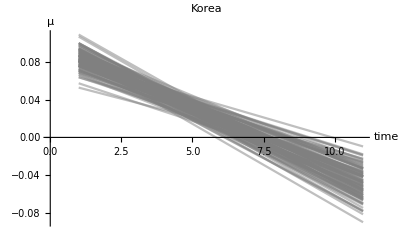

```mathematica
ListPlot[Table[QS[[i,1]] t + QS[[i,2]],{i,1,Length[QS],Length[QS]/100}],Joined -> True,Ticks->{None,Automatic},AxesLabel->{"time","μ"},PlotStyle->Directive[Opacity[0.5],Gray],PlotLabel->"Korea"]
```

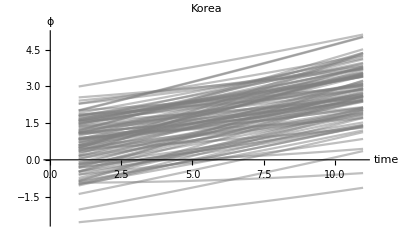

```mathematica
ListPlot[Table[QS[[i,3]] t + QS[[i,4]]+QS[[i,5]] t^2,{i,1,Length[QS],Length[QS]/100}],Joined -> True,Ticks->{None,Automatic},AxesLabel->{"time","ϕ"},PlotStyle->Directive[Opacity[0.5],Gray],PlotLabel->"Korea"]
```

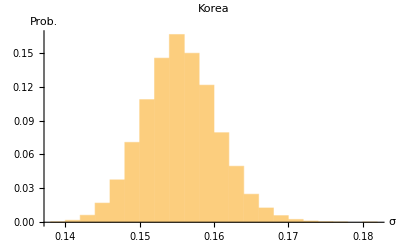

```mathematica
Histogram[Abs[QS[[All,6]]],Automatic,"Probability",AxesLabel->{"σ","Prob."},PlotLabel->"Korea"]
```